# Analytics of the L2 points (x<0)

Author : Martin Horvat, March 2016

## Definitions

```mathematica
(* Omega = delta*KopalPotential(x = delta t, y=0, z=0), a = F^2 delta^3 *)
Clear[Omega];
Omega[t_,q_,a_]:=1/Abs[t]+q(1/Abs[1-t] -t)+1/2 a(1+q) t^2

(* Omega1 is Omega[-t], for t > 0 *)
Clear[Omega2];
Omega2[t_,q_,a_]:=1/t+q(1/(1+t) + t)+1/2 a(1+q) t^2

(* Derivative Omega2 *)
Clear[dOmega2];
dOmega2[t_,q_,a_]=Together[D[Omega2[t,q,a],t]]
```

(-1-2 t-t^2+a t^3+2 q t^3+a q t^3+2 a t^4+q t^4+2 a q t^4+a t^5+a q t^5)/(t^2 (1+t)^2)

```mathematica
(* Polynomials *)
```

```mathematica
Clear[P];
P[t_,q_,a_]=Simplify[-Numerator[dOmega2[t,q,a]]]
```

1+2 t+t^2-(a+2 q+a q) t^3-(q+2 a (1+q)) t^4-a (1+q) t^5

```mathematica
CForm[HornerForm[P[t,q,a]/.a->c/(1+q),t]]
```

1 + t*(2 + t*(1 + t*(-c - 2*q + t*(-2*c - q - c*t))))

```mathematica
CForm[HornerForm[D[P[t,q,a]/.a->c/(1+q),t],t]]
```

2 + t*(2 + t*(-3*c - 6*q + t*(-8*c - 4*q - 5*c*t)))

```mathematica
(* Note: s in [0,1] *)
Clear[Q];
Q[s_,q_,a_]=Simplify[Numerator[Together[dOmega2[s/(1-s),q,a]]]]
```

1-3 s+3 s^2-(1+a+2 q+a q) s^3+3 q s^4-q s^5

```mathematica
CForm[HornerForm[Q[t,q,a]/.(1+a+2 q+a q)->c,t]]
```

1 + t*(-3 + t*(3 + t*(-c + t*(3*q - q*t))))

```mathematica
CForm[HornerForm[D[Q[t,q,a]/.(1+a+2 q+a q)->c,t],t]]
```

-3 + t*(6 + t*(-3*c + t*(12*q - 5*q*t)))

```mathematica
Solve[s/(1-s)==t,s]
```

{{s→t/(1+t)}}

```mathematica
(* Solution *)
```

```mathematica
Clear[Sol]
Sol[q_,a_]:=Module[{t},First[t/.Solve[{P[t,q,a]==0,t>0},t,Reals]]];
```

## Plots

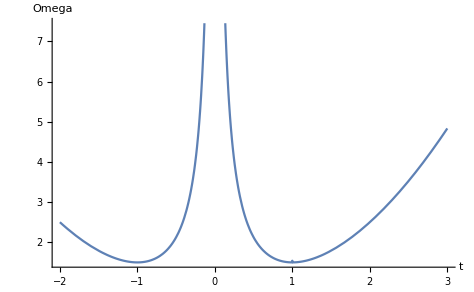

```mathematica
Plot[Omega[t,0.00001,1],{t,-2,3},AxesLabel->{"t","Omega"}]
```

```mathematica
w
```

```mathematica
Sol[0.1,0.1]
```

1.85229

```mathematica
FindMinimum[Omega[t,0.1,10],{t,-0.7}]
```

{3.44988,{t→-0.448065}}

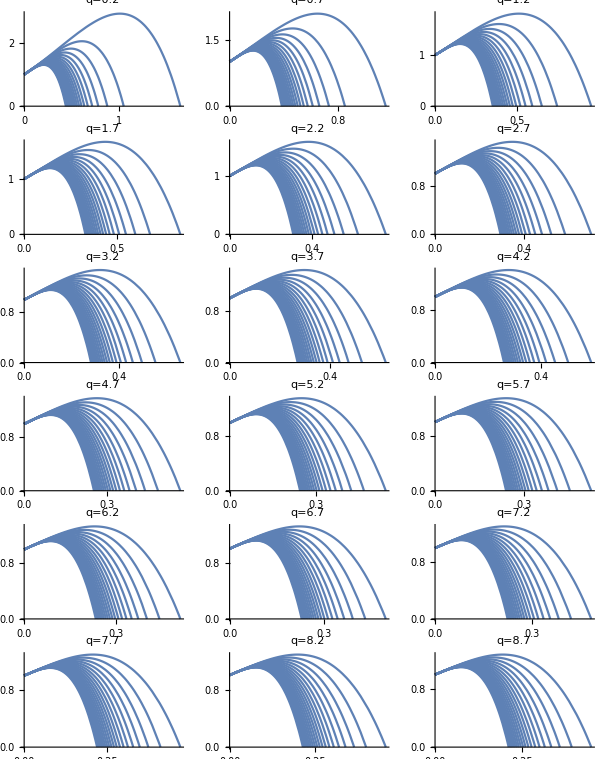

```mathematica
GraphicsGrid[
Partition[Table[
Plot[
Table[P[t,q,a],{a,0.1,10,0.5}],
{t,0,4},
PlotRange->{All,{0,Automatic}},
PlotLabel->"q="<>ToString[q],
PlotLabel->{"t","P(t;q,a)"}
],
{q,0.2,10,0.5}],
3
]
]
```

Comment : It is clear that there is only one positive zero!

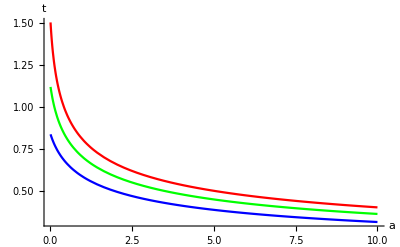

```mathematica
Plot[{Sol[0.5,a],Sol[1,a],Sol[2,a]},{a,0.01,10},PlotRange->All,PlotStyle->{Red,Green,Blue},AxesLabel->{"a","t"}]
```

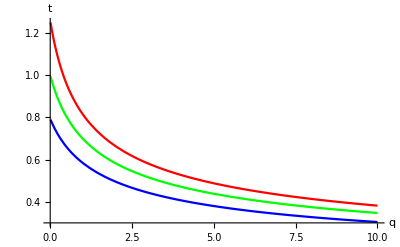

```mathematica
Plot[{Sol[q,0.5],Sol[q,1],Sol[q,2]},{q,0.01,10},PlotRange->All,PlotStyle->{Red,Green,Blue},AxesLabel->{"q","t"}]
```

## a = 1

```mathematica
CForm[HornerForm[P[x,q,1],x]]
```

1 + x*(2 + x*(1 + x*(-1 - 3*q + x*(-2 - 3*q + (-1 - q)*x))))

```mathematica
CForm[HornerForm[D[P[x,q,1],x],x]]
```

2 + x*(2 + x*(-3 - 9*q + x*(-8 - 12*q + (-5 - 5*q)*x)))

```mathematica
CForm[HornerForm[P[1-x,q,1],x]]
```

-7*q + x*(12 + 26*q + x*(-24 - 37*q + x*(19 + 25*q + x*(-7 - 8*q + (1 + q)*x))))

```mathematica
CForm[HornerForm[D[P[1-x,q,1],x],x]]
```

12 + 26*q + x*(-48 - 74*q + x*(57 + 75*q + x*(-28 - 32*q + (5 + 5*q)*x)))

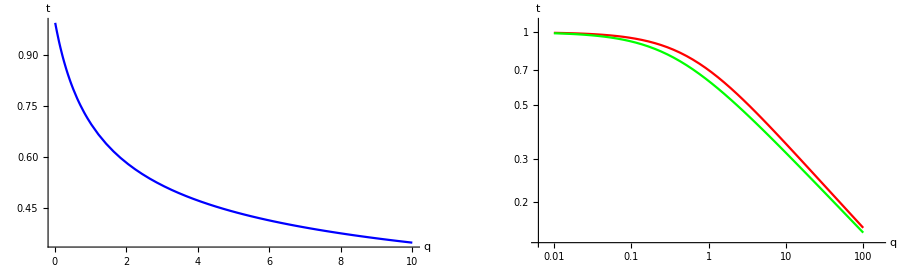

```mathematica
GraphicsGrid[
{{Plot[Sol[q,1],{q,0.01,10},PlotRange->All,PlotStyle->Blue,AxesLabel->{"q","t"}],
LogLogPlot[{Sol[q,1],1/(3q+1)^(1/3)},{q,0.01,100},PlotRange->All,PlotStyle->{Red,Green},AxesLabel->{"q","t"}]}}]
```

### q -> ∞

Using Q :  q -> infty

t=s/(1-s)
Q(s,q) = Q1(s) + q Q2(s) =0	Q1(s) = Q(s,0)

1/q=-Q2/Q1(s) = R1(s)

```mathematica
B[s_,p_]=Q[s,p,1];
Q1[s_]=B[s,0]
Q2[s_]=Simplify[D[B[s,p],p]]
```

1-3 s+3 s^2-2 s^3

-s^3 (3-3 s+s^2)

```mathematica
R1[s_]=-Q2[s]/Q1[s]
```

(s^3 (3-3 s+s^2))/(1-3 s+3 s^2-2 s^3)

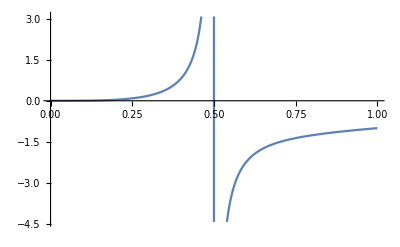

```mathematica
Plot[R1[s],{s,0,1}]
```

```mathematica
H1[w_]=Normal[Series[Simplify[Normal[InverseSeries[Series[R1[s],{s,0,12}],z]]/.z->3w^3,w>0],{w,0,8}]]
```

w-(2 w^2)/3+(2 w^3)/9-(22 w^4)/81+(4 w^5)/243+(2 w^6)/9+(542 w^7)/6561+(1172 w^8)/19683

```mathematica
CForm/@N[Rest[CoefficientList[H1[w],w]]]
```

{1.,-0.6666666666666666,0.2222222222222222,-0.2716049382716049,0.01646090534979424,0.2222222222222222,0.08260935832952294,0.05954376873444089}

```mathematica
HornerForm[Sum[c[i-1]w^i,{i,1,8}],w]
```

w (c[0]+w (c[1]+w (c[2]+w (c[3]+w (c[4]+w (c[5]+w (c[6]+w c[7])))))))

```mathematica
Block[{w,q,s,p},
q=100.;
p=q;
w=(3p)^(-1/3);
s=H1[w];
{s,s/(1-s),Sol[q,1]}
]
```

{0.135113,0.156221,0.156221}

Trying to tune the series!!!

```mathematica
Clear[Y,Y1,Y2,D1,K1]
Y[s_,b_]=Q[s,b-i,1];
Y1[s_]=Y[s,0];
Y2[s_]=Simplify[D[Y[s,b],b]];
D1[s_]=Simplify[-Y2[s]/Y1[s]];
K1[w_]=Series[Simplify[Normal[InverseSeries[Series[D1[s],{s,0,12}],z]]/.z->3w^3,w>0],{w,0,8}]
```

w-(2 w^2)/3+(2 w^3)/9+(-22/81+i) w^4+(4/243-(4 i)/3) w^5+(2/9+(2 i)/3) w^6+(542/6561-(88 i)/81+2 i^2) w^7-(2 (-586-810 i+32805 i^2) w^8)/19683+O[w]^9

```mathematica
Solve[4/243-(4 i)/3==0,i]
Solve[2/9+(2 i)/3==i,i]
```

{{i→1/81}}

{{i→2/3}}

Trying to use P:

```mathematica
T[t_,p_]=P[t,p-k,1];
T1[t_]=T[t,0]
T2[t_]=Simplify[D[T[t,p],p]]
```

1+2 t+t^2-(1-3 k) t^3-(2 (1-k)-k) t^4-(1-k) t^5

-t^3 (3+3 t+t^2)

```mathematica
R11[t_]=-T2[t]/T1[t]
```

(t^3 (3+3 t+t^2))/(1+2 t+t^2-(1-3 k) t^3-(2 (1-k)-k) t^4-(1-k) t^5)

```mathematica
R11[t]/.k->1
```

(r^3 (3+3 r+r^2))/(1+2 r+r^2+2 r^3+r^4)

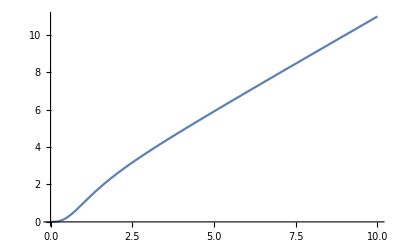

```mathematica
Plot[R11[t]/.k->1,{t,0,10}]
```

```mathematica
H11[w_]=Normal[Series[Simplify[Normal[InverseSeries[Series[R11[t],{t,0,12}],z]]/.z->3w^3,w>0],{w,0,8}]]
```

w+w^2/3-w^3/9+(-31/81+k) w^4+(-119/243+(2 k)/3) w^5+(-1/9-k/3) w^6+(3089/6561-(124 k)/81+2 k^2) w^7+((14849-48195 k+32805 k^2) w^8)/19683

```mathematica
Block[{w,q,s,p,kk,t},
q=2.77;
kk=1.;
p=q+kk;
w=(3p)^(-1/3);
t=H11[w]/.k->kk;
{t,Sol[q,1]}
]
```

{0.529006,0.528681}

```mathematica
CForm/@N[Rest[CoefficientList[H11[w]/.k->1,w]]]
```

{1.,0.3333333333333333,-0.1111111111111111,0.6172839506172839,0.17695473251028807,-0.4444444444444444,0.9399481786313062,-0.027485647513082356}

```mathematica
1.5
```

```mathematica
1-0.471319
```

0.528681

### q → 0

Using F(s,q) = P(1/(1 + s), q) : q->0

F(s,q) = F1(s) + q F2(s) = 0

t = 1/(1+s)

R(s) = -F1(s)/F2(s) = q

```mathematica
F[s_,q_]=Collect[Expand[Numerator[Together[-P[1/(1+s),q,1]]]],s,Simplify]
```

7 q+(-12+9 q) s+3 (-8+q) s^2-19 s^3-7 s^4-s^5

```mathematica
F1[s_]=F[s,0]
F2[s_]=D[F[s,q],q]
R2[s]=-F1[s]/F2[s]
```

-12 s-24 s^2-19 s^3-7 s^4-s^5

7+9 s+3 s^2

(12 s+24 s^2+19 s^3+7 s^4+s^5)/(7+9 s+3 s^2)

```mathematica
H2[q_]=Normal[Series[Simplify[Normal[InverseSeries[Series[R2[s],{s,0,12}],q]],q>0],{q,0,8}]]
```

(7 q)/12-(35 q^2)/144+(3227 q^3)/20736-(1015 q^4)/9216+(308777 q^5)/3981312-(10683659 q^6)/214990848+(121753415 q^7)/5159780352+(427489013 q^8)/247669456896

```mathematica
CForm/@N[Rest[CoefficientList[H2[q],q]]]
```

{0.5833333333333334,-0.24305555555555555,0.15562307098765432,-0.1101345486111111,0.07755659440907922,-0.049693552536710775,0.023596627510085143,0.0017260465555892458}

```mathematica
Block[{w,q,s},
q=0.9;
s=H2[q];
{1/(1+s),Sol[q,1]}
]
```

{0.713913,0.715464}

Using P:

P(1-u,q,1) = P1(u) + q P2(u) = 0

t=1-u

R(s) = -P1(s)/P2(s) = q

```mathematica
P1[u_]=Simplify[P[1-u,0,1]]
P2[u_]=Simplify[D[P[1-u,q,1],q]]
R3[u_]=-P1[u]/P2[u]
```

(-2+u)^2 u (3-3 u+u^2)

(-1+u)^3 (7-5 u+u^2)

-((-2+u)^2 u (3-3 u+u^2))/((-1+u)^3 (7-5 u+u^2))

```mathematica
H3[q_]=Normal[InverseSeries[Series[R3[u],{u,0,8}],q]]
```

(7 q)/12-(7 q^2)/12+(13223 q^3)/20736-(177835 q^4)/248832+(9608543 q^5)/11943936-(387585233 q^6)/429981696+(5163003559 q^7)/5159780352-(90578991167 q^8)/82556485632

```mathematica
CForm/@N[Rest[CoefficientList[H3[q],q]]]
```

{0.5833333333333334,-0.5833333333333334,0.6376832561728395,-0.7146789801954733,0.8044704023866169,-0.901399377242328,1.0006246791103715,-1.097175957450039}

```mathematica
Block[{w,q,u},
q=0.5;
u=H3[q];
{1-u,Sol[q,1]}
]
```

{0.804537,0.803028}

Comment : The expansion in P is not good!

### q ≈ 1

Using P:

t = t0 + u
q = 1 + 	e => e = q-1

P(t,q) = P1(t) +P2(t) e,		P1(t) =  P(t,1);

R(u) = -P1(t0+u)/P2(t0+u) = e

```mathematica
t01=Sol[1,1.]
```

0.698406

```mathematica
P3[t_]=Simplify[P[t,1,1]]
P4[t_]=(Simplify[P[t,q,1]-P3[t]])/(q-1)
R3[t_]=-P3[t]/P4[t]
```

1+2 t+t^2-4 t^3-5 t^4-2 t^5

-t^3 (3+3 t+t^2)

-(-1-2 t-t^2+4 t^3+5 t^4+2 t^5)/(t^3 (3+3 t+t^2))

```mathematica
DR3=FullSimplify[Table[D[R3[t],{t,n}]/n!,{n,1,8}]]/.t->t01
```

{-6.12483,15.9757,-36.295,75.3831,-147.377,275.93,-500.099,883.704}

```mathematica
H4[e_]=Normal[InverseSeries[SeriesData[u,0,DR3,1,Length[DR3]+1,1],e]]
```

-0.16327 e+0.0695311 e^2-0.0334307 e^3+0.0168794 e^4-0.00873408 e^5+0.00458096 e^6-0.00242135 e^7+0.00128542 e^8

```mathematica
CForm/@Rest[CoefficientList[Normal[H4[e]],e]]
```

{-0.16326993510260143,0.06953110611033309,-0.033430671075654735,0.01687940218811356,-0.008734076561902074,0.004580958503437698,-0.0024213475610572683,0.0012854157986699256}

```mathematica
Block[{q,e,u},
q=2.;
e=q-1;
u=H4[e];
{t01+u,Sol[q,1]}
]
```

{0.582827,0.582381}

## q = 1

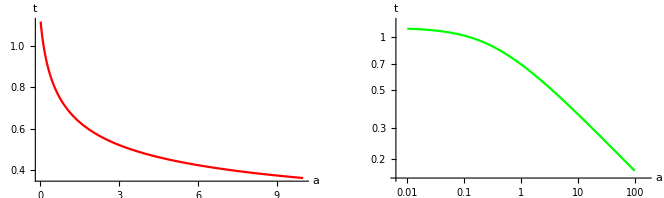

```mathematica
GraphicsGrid[
{
{
Plot[Sol[1,a],{a,0.01,10},PlotRange->All,PlotStyle->Red,AxesLabel->{"a","t"}],
LogLogPlot[Sol[1,a],{a,0.01,100},PlotRange->All,PlotStyle->{Red,Green},AxesLabel->{"a","t"}]
}
}]
```

```mathematica
Sol[1.,0]
```

1.13224

### a -> ∞

Using Q:

t = s/(1 - s)

Q[s,1,a] = Q1[s]- 2a s^3 = 0

R(s) = s^3/Q1[s] = 1/(2a)

```mathematica
Q3[s_]=Simplify[Q[s,1,0]]
Q4[s_]=Simplify[Q[s,1,a]-Q[s,1,0]]/(2a)
R4[s_]=-Q4[s]/Q3[s]
```

1-3 s+3 s^2-3 s^3+3 s^4-s^5

-s^3

s^3/(1-3 s+3 s^2-3 s^3+3 s^4-s^5)

```mathematica
H5[w_]=Normal[Series[Simplify[Normal[InverseSeries[Series[R4[s],{s,0,12}],z]]/.z->w^3,w>0],{w,0,8}]]
```

w-w^2+w^3-(5 w^4)/3+(10 w^5)/3-(19 w^6)/3+(107 w^7)/9-(209 w^8)/9

```mathematica
Block[{q,w,a,s},
q=1.;
a=2.;
w=(2a)^(-1/3);
s=H5[w];
{s/(1-s),Sol[q,a]}
]
```

{0.0499939,0.583631}

Tunning the series!!!

```mathematica
W[s_,b_]=Q[s,1,a]/.(3+2a)->b-2
```

1-3 s+3 s^2-(-2+b) s^3+3 s^4-s^5

```mathematica
W1[s_]=Simplify[W[s,0]]
W2[s_]=Simplify[W[s,b]-W[s,0]]/b
```

1-3 s+3 s^2+2 s^3+3 s^4-s^5

-s^3

```mathematica
R5[s_]=s^3/W1[s]
```

s^3/(1-3 s+3 s^2+2 s^3+3 s^4-s^5)

```mathematica
H6[w_]=Normal[Series[Simplify[Normal[InverseSeries[Series[R5[s],{s,0,12}],z]]/.z->w^3,w>0],{w,0,3}]]
```

w-w^2+w^3

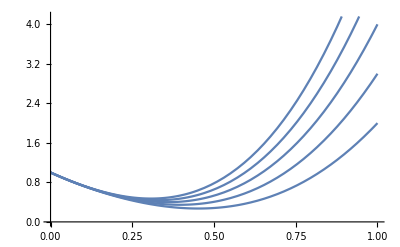

```mathematica
Plot[Table[Q[s,1,a]/.(3+2a)->-b,{b,-1,3}],{s,0,1},PlotRange->{All,{0,Automatic}}]
```

```mathematica
Block[{q,w,a,s},
q=1.;
a=2.;
w=(2a+5)^(-1/3);
s=H6[w];
{s/(1-s),Sol[q,a]}
]
```

{0.56431,0.583631}

### a -> 0

Using Q:

Q(s,1,a) = Q1(s) + a Q2(s)

R= -Q1/Q2

t= s/(1-s)

Q(s0,1,0) = 0 

s= s0 + u

```mathematica
t02=Sol[1.,0]
```

1.13224

```mathematica
FullSimplify[Q[s,1,0]]
```

-(-1+s) (1+(-2+s) s (1+s^2))

```mathematica
S01=s/.Solve[1+(-2+s) s (1+s^2)==0,s]
```

{1/2+1/(√2)-1/2 √(-1+2 √2),1/2+1/(√2)+1/2 √(-1+2 √2),1/2 (1-√2-ⅈ √(1+2 √2)),1/2 (1-√2+ⅈ √(1+2 √2))}

```mathematica
s01=1/2+1/(√2)-1/2 √(-1+2 √2);
```

```mathematica
N[s01]
```

0.53101

```mathematica
N[s01/(1-s01)]
```

1.13224

```mathematica
R6[s_]=-Q[s,1,0]/D[Q[s,1,a],a]
```

-(-1+3 s-3 s^2+3 s^3-3 s^4+s^5)/(2 s^3)

```mathematica
H7[a_]=Normal[InverseSeries[(N[Sum[D[R6[s],{s,n}]u^n/n!,{n,1,8}]/.s->s01])+O[u]^9,a]]
```

-0.314404 a+0.74518 a^2-2.5574 a^3+10.3934 a^4-46.4802 a^5+220.992 a^6-1096.31 a^7+5610.77 a^8

```mathematica
Block[{q,a,s},
q=1;
a=0.01;
s=s01+H7[a];
{s/(1-s),Sol[q,a]}
]
```

{1.11837,1.11837}

```mathematica
CForm/@Rest[CoefficientList[H7[a],a]]
```

{-0.3144040531308815,0.7451796412511179,-2.5574013258834385,10.393413194099757,-46.480222635440576,220.992329719314,-1096.31143523615,5610.772061807706}

```mathematica
t02=FullSimplify[s01/(1-s01)]
```

1/2 (-1+√(5+4 √2))

Using P:

P(t,1,a) = P1(t) + a P2(s)

R= -P1/P2

P(t0,1,0) = 0

t=t02 + u

```mathematica
R7[t_]=Simplify[-P[t,1,0]/D[P[t,1,a],a]]
```

(1+2 t+t^2-2 t^3-t^4)/(2 t^3 (1+t)^2)

```mathematica
H8[a_]=Normal[InverseSeries[(N[Sum[D[R7[t],{t,n}]u^n/n!,{n,1,8}]/.t->t02])+O[u]^9,a]]
```

-1.42942 a+4.34619 a^2-16.812 a^3+73.224 a^4-342.499 a^5+1680.34 a^6-8531.17 a^7+44444.2 a^8

```mathematica
Block[{q,a,u},
q=1;
a=0.1;
u=H8[a];
{t02+u,Sol[q,a]}
]
```

{1.02112,1.02096}

Comment : It does not work better!

### a ≈ 1

Using P :
   
   P (t, 1, 1+e) = P1 (t) + e P2 (s)
   
   R= -P1/P2
   
   P (t0, 1, 1) = 0
   
   a=1 + e
   t = t0 + u

```mathematica
t03=Sol[1,1.]
```

0.698406

```mathematica
R8[t_]=Simplify[-P[t,1,1]/D[P[t,1,1+e],e]]
```

(1+2 t+t^2-4 t^3-5 t^4-2 t^5)/(2 t^3 (1+t)^2)

```mathematica
H9[a_]=Normal[InverseSeries[(N[Sum[D[R8[t],{t,n}]u^n/n!,{n,1,8}]/.t->t03])+O[u]^9,a]]
```

-0.168715 a+0.085348 a^2-0.0516052 a^3+0.0339528 a^4-0.0234878 a^5+0.0168027 a^6-0.0123144 a^7+0.00919176 a^8

```mathematica
CForm/@Rest[CoefficientList[H9[a],a]]
```

{-0.1687145366373403,0.08534802424313279,-0.051605226945983546,0.03395282072634135,-0.02348777505462479,0.016802697645681368,-0.012314365592402357,0.009191764021482736}

```mathematica
Block[{q,a,u,e},
q=1;
a=2.;
e=a-1;
u=H9[e];
{t03+u,Sol[q,a]}
]
```

{0.58758,0.583631}

## a != 1, q != 1

### a → ∞

U1[s_, q_, b_] = Q[s, q, a]
 
b = 1 + a + 2 q + a q
Q = U1 + b U2 =

R= -U2/U1  = 1/b

```mathematica
Clear[U,U1,U2,k]

U[s_,q_,b_]=Q[s,q,a]/.(1+a+2 q+a q)->b-k
U1[s_,q_]=U[s,q,0]
U2[s_,q_]=D[U[s,q,b],b]
R9[s_,q_]= - U2[s,q]/U1[s,q]
```

1-3 s+3 s^2-(b-k) s^3+3 q s^4-q s^5

1-3 s+3 s^2+k s^3+3 q s^4-q s^5

-s^3

s^3/(1-3 s+3 s^2+k s^3+3 q s^4-q s^5)

```mathematica
H10[w_,q_]=Normal[Series[Simplify[Normal[InverseSeries[Series[R9[s,q],{s,0,12}],z]]/.z->w^3,w>0],{w,0,3}]]
```

w-w^2+w^3

```mathematica
Block[{q,w,a,b,s,kk,x,y},
q=10;
a=0.1;
kk=2;
b=1+k+2 q+a(1+ q)/.k->kk;
w=b^(-1/3);
s=H10[w,q]/.k->kk;
x=s/(1-s);
y=Sol[q,a];
{x,y,(x-y)/y}
]
```

{0.454754,0.424807,0.0704952}

```mathematica
HornerForm[H10[w,q]/.k->0,w]
```

w (1+w (-1+w (1+w (-2/3+w (1/3+q+w (-(10 q)/3+w (-1/9+(22 q)/3+(1/9-(35 q)/3) w)))))))

```mathematica
HornerForm[H10[w,q]/.k->2,w]
```

w (1+w (-1+w (1+w^2 (-1+q+w (2-(10 q)/3+w (-1+(22 q)/3+(-1-(25 q)/3) w))))))

### q→ ∞

Q[s, q, a] = J1[s,a] + q J2[s,a]
 
R= -J2/J1  = 1/q

t= s/(1-s)

```mathematica
J1[s_,a_]=Q[s,0,a]
J2[s_,a_]=Simplify[D[Q[s,q,a],q]]
R11[s_,a_]=-J2[s,a]/J1[s,a]
```

1-3 s+3 s^2-(1+a) s^3

-s^3 (2+a-3 s+s^2)

(s^3 (2+a-3 s+s^2))/(1-3 s+3 s^2-(1+a) s^3)

```mathematica
H11[w_,q_]=Normal[FullSimplify[Series[Simplify[Normal[InverseSeries[Series[R11[s,a],{s,0,12}],z]]/.z->(2 +a)w^3,w>0&&a>0],{w,0,8}]]]
```

w+(-1+1/(2+a)) w^2+((1+a (2+3 a)) w^3)/(3 (2+a)^2)+((1-a (5+a (1+a) (8+a))) w^4)/(3 (2+a)^3)+((-2+2 a (-16+a (-4+3 a (1+a (7+a))))) w^5)/(9 (2+a)^4)+((-1+a (3+a (64+a (64+a (48-a (13+3 a)))))) w^6)/(3 (2+a)^5)+((20+a (480+a (3408+a (1006+9 a (35+a (-196+a (119+2 a (18+a)))))))) w^7)/(81 (2+a)^6)+((35+a (-91+a (3024+a (-4187+a (2824-3 a (-730+a (-2698+3 a (79+5 a (13+a))))))))) w^8)/(81 (2+a)^7)

```mathematica
Block[{q,w,a,s,x,y},
q=0.01;
a=0.01;
w=((2+a)q)^(-1/3);
s=H11[w,q];
x=s/(1-s);
y=Sol[q,a];
{x,y,(x-y)/y}
]
```

{-1.00817,4.32872,-1.2329}

```mathematica
CForm/@Rest[HornerForm/@CoefficientList[Series[H11[3(2+a) z,q]/(2+a),{z,0,8}],z]]
```

{3,-9 - 9*a,9 + a*(18 + 27*a),27 + a*(-135 + a*(-216 + (-243 - 27*a)*a)),-54 + a*(-864 + a*(-216 + a*(162 + a*(1134 + 162*a)))),-243 + a*(729 + a*(15552 + a*(15552 + a*(11664 + (-3159 - 729*a)*a)))),540 + a*(12960 + a*(92016 + a*(27162 + a*(8505 + a*(-47628 + a*(28917 + a*(8748 + 486*a))))))),2835 + a*(-7371 + a*(244944 + a*(-339147 + a*(228744 + a*(177390 + a*(655614 + a*(-57591 + (-47385 - 3645*a)*a)))))))}

### a -> 0

#### Try 1

Due to the fact that L2 divergences for small a in the limit q -> 0, we use Q.

Q(s,q,a) = Q(s,q,a=0) - b s^3
b=a(1+q)

b= Q(s,q,a=0)/s^3 = R(s)

R(s_0) = 0

=>

b= R(s_0 + u) = series in u

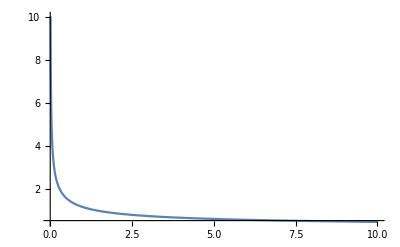

```mathematica
Plot[Sol[q,0],{q,0.01,10},PlotRange->All]
```

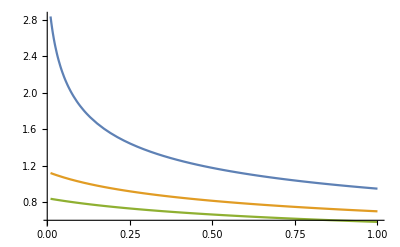

```mathematica
Plot[{
Sol[0.1,a],
Sol[1,a],
Sol[2,a]},
{a,0.01,1},PlotRange->All]
```

```mathematica
P[t,q,0]
```

1+2 t+t^2-2 q t^3-q t^4

```mathematica
T1=Simplify[t/.Solve[P[t,q,0]==0,t],q>0]
```

{1/6 (-3-√3 √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))-3 √(2+4/(3 q)-1/(3 q (-1-54 q^2-6 q √(3+81 q^2))^(1/3))-((-1-54 q^2-6 q √(3+81 q^2))^(1/3))/(3 q)+(2 √3 (-1+q))/(q √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))))),1/6 (-3-√3 √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))+3 √(2+4/(3 q)-1/(3 q (-1-54 q^2-6 q √(3+81 q^2))^(1/3))-((-1-54 q^2-6 q √(3+81 q^2))^(1/3))/(3 q)+(2 √3 (-1+q))/(q √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))))),1/6 (-3+√3 √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))-3 √(2+4/(3 q)-1/(3 q (-1-54 q^2-6 q √(3+81 q^2))^(1/3))-((-1-54 q^2-6 q √(3+81 q^2))^(1/3))/(3 q)-(2 √3 (-1+q))/(q √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))))),1/6 (-3+√3 √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3)))+3 √(2+4/(3 q)-1/(3 q (-1-54 q^2-6 q √(3+81 q^2))^(1/3))-((-1-54 q^2-6 q √(3+81 q^2))^(1/3))/(3 q)-(2 √3 (-1+q))/(q √(3+((1+(-1-54 q^2-6 q √(3+81 q^2))^(1/3))^2)/(q (-1-54 q^2-6 q √(3+81 q^2))^(1/3))))))}

```mathematica
T1/.q->0.1
```

{-3.4609-1.66533×10^-16 ⅈ,-0.896285-0.291167 ⅈ,-0.896285+0.291167 ⅈ,3.25347+5.55112×10^-17 ⅈ}

```mathematica
Simplify[Q[s,q,0]/(1-s)]
```

1-2 s+s^2-2 q s^3+q s^4

```mathematica
S1=s/.Solve[-1+2 s-s^2+2 q s^3-q s^4==0,s]
```

{1/2-(√(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))/(2 √3)-1/2 √(2-4/(3 q)-1/(3 q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))-((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/(3 q)-(√3 (8+8/q))/(4 √(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))),1/2-(√(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))/(2 √3)+1/2 √(2-4/(3 q)-1/(3 q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))-((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/(3 q)-(√3 (8+8/q))/(4 √(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))),1/2+(√(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))/(2 √3)-1/2 √(2-4/(3 q)-1/(3 q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))-((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/(3 q)+(√3 (8+8/q))/(4 √(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))),1/2+(√(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q))/(2 √3)+1/2 √(2-4/(3 q)-1/(3 q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))-((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/(3 q)+(√3 (8+8/q))/(4 √(3-2/q+1/(q (1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2-6 √3 √(q^2+27 q^4))^(1/3))/q)))}

```mathematica
QSol0[q_]:=Module[{f1,f2},
f1=(1+54 q^2-6 √3 q √(1+27 q^2))^(1/3);
f2=(3-2/q+1/(q f1)+f1/q)/3;

1/2+Sqrt[f2]/2-1/2Sqrt[3-2/q-f2+2(1+1/q)/Sqrt[f2]]
];
```

```mathematica
N[QSol0[10^-4]]
```

0.990099

```mathematica
S1/.q->0.1
```

{-0.0856265-3.04775 ⅈ,-0.0856265+3.04775 ⅈ,0.764898,1.40636}

```mathematica
Block[{q,f1,f2},
f1=(1+54 q^2-6 √3 q √(1+27 q^2))^(1/3);
f2=(3-2/q+1/(q f1)+f1/q)/3;

Normal[
Series[1/2+Sqrt[f2]/2-1/2Sqrt[3-2/q-f2+2(1+1/q)/Sqrt[f2]]/.q->u^2,{u,0,8}]
]
]
```

1-u+u^2-u^3/2-u^4+(29 u^5)/8-6 u^6+(59 u^7)/16+11 u^8

```mathematica
CForm[HornerForm[1-u+u^2-u^3/2-u^4+(29 u^5)/8-6 u^6+(59 u^7)/16+11 u^8,u]]
```

```mathematica
1 + u*(-1 + u*(1 + u*(-0.5 + u*(-1 + u*(3.625 + u*(-6 + u*(3.6875 + 11*u)))))))
```

```mathematica
Block[{q,u,s},
q=10.^-4;
u=Sqrt[q];
s=1-u+u^2-u^3/2-u^4+(29 u^5)/8-6 u^6+(59 u^7)/16+11 u^8;
{s,s/(1-s),QSol0[q]}]
```

```mathematica
Simplify[2(1/2+Sqrt[f2]/2-1/2Sqrt[3-2/q-f2+2(1+1/q)/Sqrt[f2]])]
```

1+√f2-√(3-f2+(2 (1+1/q))/(√f2)-2/q)

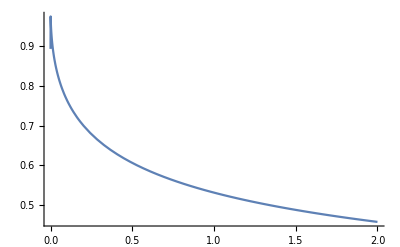

```mathematica
Plot[S1[[3]],{q,0,2}]
```

Creating inverse series

```mathematica
Simplify[Q[s,q,0]/(Q[s,q,a]-Q[s,q,0])]
```

((-1+s) (1-2 s+s^2-2 q s^3+q s^4))/(a (1+q) s^3)

```mathematica
R12[s_,q_]=Q[s,q,0]/s^3
```

(1-3 s+3 s^2-(1+2 q) s^3+3 q s^4-q s^5)/s^3

```mathematica
DR12[s_,q_]=FullSimplify[Table[D[R12[s,q]/k!,{s,k}],{k,1,8}]]
```

{q (3-2 s)-(3 (-1+s)^2)/s^4,(6-s (9-3 s+q s^4))/s^5,(-10-3 (-4+s) s)/s^6,(3 (5+(-5+s) s))/s^7,-(3 (7+(-6+s) s))/s^8,(28+3 (-7+s) s)/s^9,-(3 (-6+s) (-2+s))/s^10,(3 (15+(-9+s) s))/s^11}

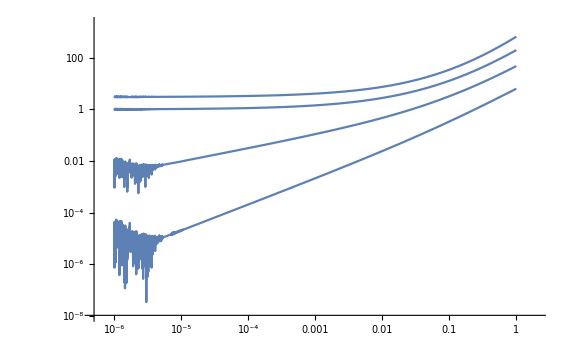

```mathematica
LogLogPlot[Take[Abs[DR12[QSol0[q],q]],4],{q,10^-6,1}]
```

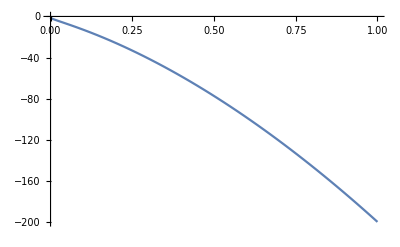

```mathematica
Plot[DR12[QSol0[q],q][[3]],{q,10^-6,1}]
```

```mathematica
SeriesData[u,0,DR12[s,q],1,5,1]/.{q->0.1,s->QSol0[0.1]}
```

-0.337398 u+6.45416 u^2-77.1879 u^3+827.492 u^4+O[u]^5

```mathematica
InverseSeries[SeriesData[u,0,DR12[s,q],1,5,1],z]/.{q->0.1,s->QSol0[0.1]}
```

-2.96386 z+168.04 z^2-13098.2 z^3+1.20154×10^6 z^4+O[z]^5

```mathematica
Block[{q,s0,F,u,z,a,b,s,ds,t0},
q=2.;
a=0.01;

b=a*(1+q);
s0=QSol0[q];

F=DR12[s0,q];
ds=Normal[InverseSeries[SeriesData[u,0,F,1,Length[F]+1,1],z]]/.z->b;

s=s0+ds;
{s0,s0+ds,s/(1-s),Sol[q,a]}
]
```

{0.457109,0.45527,0.835771,0.835771}

Comment : This is not good. Useful only for q  far away from 0 and a << 1.

```mathematica
(*without first two derivatives*)
```

```mathematica
Block[{q,s0,F,u,z,a,b,s,ds,t0},
q=10.;
a=0.01;

b=a*(1+q);
s0=QSol0[q];

F=DR12[s0,q];
F[[1]]=F[[2]]=0;
F=F*Table[(-1)^k,{k,1,Length[F]}];
ds=Normal[InverseSeries[SeriesData[u,0,F,1,Length[F]+1,1],z]]/.z->b;

s=s0-ds;
{s0,s0-ds,s/(1-s),Sol[q,a]}
]
```

{0.305361,0.282549,0.393824,0.438011}

#### Try 2

Trying another parametrization!

```mathematica
Z1[s_,q_,a_]=Numerator[Together[P[1/(1-s),q,a]]]
```

-4+4 a+3 q+4 a q+16 s-4 a s-5 q s-4 a q s-25 s^2+a s^2+2 q s^2+a q s^2+19 s^3-7 s^4+s^5

```mathematica
RZ1[s_,q_]=Simplify[-Z1[s,q,0]/D[Z1[s,q,a],a]]
```

-((-1+s) (q (-3+2 s)+(2-3 s+s^2)^2))/((1+q) (-2+s)^2)

```mathematica
DZ1[s_,q_]=Simplify[Table[D[RZ1[s,q],{s,k}]/k!,{k,1,3}]]
```

{(-3 (-2+s)^3 (-1+s)^2+q (-4+3 s))/((1+q) (-2+s)^3),-(3 (q+(-2+s)^4) (-1+s))/((1+q) (-2+s)^4),(-(-2+s)^5+q (-2+3 s))/((1+q) (-2+s)^5)}

```mathematica
Block[{q,u,t0,a,s0,s},
q=0.1;
a=0.01;
t0=Sol[q,0];
s0=(t0-1)/t0;
u=Normal[InverseSeries[SeriesData[u,0,DZ1[s0,q],1,5,1],z]]/.z->a;
s=s0+u;
{s,1/(1-s),Sol[q,a]}
]
```

{0.648968,2.84874,2.83535}

### q -> 0

Using simple iteration

```mathematica
Pb[t_,q_,b_]=Simplify[P[t,q,b/(1+q)]]
```

1+2 t+t^2-(b+2 q) t^3-(2 b+q) t^4-b t^5

```mathematica
R13[t_,q_]=Simplify[-Pb[t,0,b]/D[Pb[t,q,b],q]]
```

-((1+t)^2 (-1+b t^3))/(t^3 (2+t))

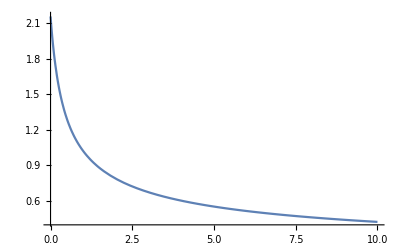

```mathematica
Plot[Sol[q,0.1],{q,10^-6,10},PlotRange->All]
```

```mathematica
Sol[0.01,0.01]
```

4.32872

```mathematica
Block[{q,a,b,t},
q=0.00001;
a=0.0001;
b=a(1+q);
t=b^(-1/3);
Do[t=(b+q*(2+t)/(1+t)^2)^(-1/3),{4}];
{t,Sol[q,a]}
]
```

{21.5111,21.5111}